```mathematica
l = 5;
h = 100;
```

```mathematica
root[n_]:= NSolve[λ * Cot[λ*l]== (h^2 - λ^2)/(2*h) &&100 * n < λ < (n+1)* 100, Reals];
lambdas = {};
For[i = 1, i <= 5, i++,lambdas=Join[lambdas,Values[root[i]]]];
lambdas
listLen = lambdas // Length
```

{{118.472},{137.35},{137.979},{138.608},{139.238},{139.867},{140.496},{141.125},{141.754},{142.383},{143.013},{143.642},{144.271},{144.9},{145.529},{146.158},{146.787},{147.416},{148.046},{148.675},{149.304},{149.933},{150.562},{151.191},{151.82},{152.449},{153.078},{153.707},{154.336},{154.965},{155.595},{156.224},{156.853},{157.482},{158.111},{158.74},{159.369},{159.998},{160.627},{161.256},{161.885},{162.514},{163.143},{163.772},{164.401},{165.03},{165.659},{166.288},{166.917},{167.546},{168.175},{168.804},{169.433},{170.062},{170.691},{171.32},{171.949},{172.578},{173.206},{173.835},{174.464},{175.093},{175.722},{176.351},{176.98},{177.609},{178.238},{178.867},{179.496},{180.125},{180.754},{181.383},{182.011},{182.64},{183.269},{183.898},{184.527},{185.156},{185.785},{186.414},{187.043},{187.671},{188.3},{188.929},{189.558},{190.187},{190.816},{191.445},{192.073},{192.702},{193.331},{193.96},{194.589},{195.218},{195.847},{196.475},{197.104},{197.733},{198.362},{198.991},{199.62},{205.908},{237.345},{237.974},{238.602},{239.231},{239.86},{240.488},{241.117},{241.746},{242.374},{243.003},{243.632},{244.26},{244.889},{245.518},{246.147},{246.775},{247.404},{248.033},{248.661},{249.29},{249.919},{250.547},{251.176},{251.805},{252.433},{253.062},{253.69},{254.319},{254.948},{255.576},{256.205},{256.834},{257.462},{258.091},{258.72},{259.348},{259.977},{260.606},{261.234},{261.863},{262.492},{263.12},{263.749},{264.377},{265.006},{265.635},{266.263},{266.892},{267.521},{268.149},{268.778},{269.406},{270.035},{270.664},{271.292},{271.921},{272.55},{273.178},{273.807},{274.435},{275.064},{275.693},{276.321},{276.95},{277.578},{278.207},{278.836},{279.464},{280.093},{280.721},{281.35},{281.979},{282.607},{283.236},{283.864},{284.493},{285.122},{285.75},{286.379},{287.007},{287.636},{288.265},{288.893},{289.522},{290.15},{290.779},{291.408},{292.036},{292.665},{293.293},{293.922},{294.55},{295.179},{295.808},{296.436},{297.065},{297.693},{298.322},{298.95},{299.579},{300.208},{337.292},{337.92},{338.549},{339.177},{339.806},{340.434},{341.063},{341.691},{342.32},{342.948},{343.577},{344.205},{344.834},{345.462},{346.091},{346.72},{347.348},{347.977},{348.605},{349.234},{349.862},{350.491},{351.119},{351.748},{352.376},{353.005},{353.633},{354.262},{354.89},{355.519},{356.147},{356.776},{357.404},{358.033},{358.661},{359.29},{359.918},{360.547},{361.175},{361.804},{362.432},{363.061},{363.689},{364.318},{364.946},{365.575},{366.203},{366.832},{367.46},{368.089},{368.717},{369.346},{369.974},{370.603},{371.231},{371.859},{372.488},{373.116},{373.745},{374.373},{375.002},{375.63},{376.259},{376.887},{377.516},{378.144},{378.773},{379.401},{380.03},{380.658},{381.287},{381.915},{382.544},{383.172},{383.801},{384.429},{385.058},{385.686},{386.315},{386.943},{387.572},{388.2},{388.828},{389.457},{390.085},{390.714},{391.342},{391.971},{392.599},{393.228},{393.856},{394.485},{395.113},{395.742},{396.37},{396.999},{397.627},{398.256},{398.884},{399.512},{436.591},{437.22},{437.848},{438.477},{439.105},{439.734},{440.362},{440.99},{441.619},{442.247},{442.876},{443.504},{444.133},{444.761},{445.389},{446.018},{446.646},{447.275},{447.903},{448.532},{449.16},{449.789},{450.417},{451.045},{451.674},{452.302},{452.931},{453.559},{454.188},{454.816},{455.444},{456.073},{456.701},{457.33},{457.958},{458.587},{459.215},{459.844},{460.472},{461.1},{461.729},{462.357},{462.986},{463.614},{464.243},{464.871},{465.499},{466.128},{466.756},{467.385},{468.013},{468.642},{469.27},{469.898},{470.527},{471.155},{471.784},{472.412},{473.041},{473.669},{474.297},{474.926},{475.554},{476.183},{476.811},{477.439},{478.068},{478.696},{479.325},{479.953},{480.582},{481.21},{481.838},{482.467},{483.095},{483.724},{484.352},{484.981},{485.609},{486.237},{486.866},{487.494},{488.123},{488.751},{489.38},{490.008},{490.636},{491.265},{491.893},{492.522},{493.15},{493.778},{494.407},{495.035},{495.664},{496.292},{496.921},{497.549},{498.177},{498.806},{499.434},{500.063},{537.139},{537.767},{538.396},{539.024},{539.652},{540.281},{540.909},{541.538},{542.166},{542.794},{543.423},{544.051},{544.68},{545.308},{545.936},{546.565},{547.193},{547.822},{548.45},{549.078},{549.707},{550.335},{550.964},{551.592},{552.22},{552.849},{553.477},{554.106},{554.734},{555.362},{555.991},{556.619},{557.248},{557.876},{558.504},{559.133},{559.761},{560.389},{561.018},{561.646},{562.275},{562.903},{563.531},{564.16},{564.788},{565.417},{566.045},{566.673},{567.302},{567.93},{568.559},{569.187},{569.815},{570.444},{571.072},{571.701},{572.329},{572.957},{573.586},{574.214},{574.843},{575.471},{576.099},{576.728},{577.356},{577.985},{578.613},{579.241},{579.87},{580.498},{581.126},{581.755},{582.383},{583.012},{583.64},{584.268},{584.897},{585.525},{586.154},{586.782},{587.41},{588.039},{588.667},{589.296},{589.924},{590.552},{591.181},{591.809},{592.437},{593.066},{593.694},{594.323},{594.951},{595.579},{596.208},{596.836},{597.465},{598.093},{598.721},{599.35},{599.978}}

506

```mathematica
Xn[λ_, x_] := λ*Cos[λ*x] - h * Sin[λ*x]


XnNormSquared[λ_, min_, max_] := Integrate[((λ*Cos[λ*w] - h * Sin[λ*w])^2), {w, min, max}]


Cn[λ_] := Integrate[(Cos[w]-1/((2-l*h))*h-1/(2-l*h)*w)* Xn[λ, w], {w, 0, l}]/XnNormSquared[λ, 0, l]


Dn[λ_] := Integrate[(2*w-(1-2*l*h)/((2-l*h)*h)-3/(2-l*h)*w)* Xn[λ, w], {w, 0, l}]/(λ * XnNormSquared[λ, 0, l])
```

```mathematica
P[x_, t_] := ∑_(n=1)^listLen (Cn[lambdas[[n]]]*Cos[lambdas[[n]]*t] + Dn[lambdas[[n]]] * Sin[lambdas[[n]]*t])* Xn[lambdas[[n]], x]

P[l - 1/h, 0]
solp = D[P[x, t], t];
solp /. {x -> 1 / (1 - (1 + h)/(1 - l *h)), t -> 0}

En[λ_] := Integrate[Cos[w]* Xn[λ, w],  {w, 0, l}]/XnNormSquared[λ, 0, l];

tEn[λ_, t_] := Exp[t] * En[λ];
```

{0.0644475}

{0.0150344}

```mathematica
Tn[λ_, t_] = tEn[λ, t] * (Cos[λ * t]/ λ^2 + Exp[t] / λ^2) - En[λ] * Sin[λ * t]/ λ^3;
```

```mathematica
Q[x_, t_] := ∑_(n=1)^listLen Tn[lambdas[[n]], t]* Xn[lambdas[[n]], x];

sol = D[Q[x, t], t];
sol /. {x -> 100, t -> 0.01}
Q[1, 0.01]
```

{-0.0000196683}

{-2.40095×10^-7}

```mathematica
omega[x_, t_] := ((1 - 2 * l * h) * t + 1)/((2 - l * h)*h) + (3 * t - 1)/(2 - l * h) * x;

omega[1,2]

u[x_, t_] := P[x, t] + Q[x, t] + omega[x, t];

u[1,0.00001]
```

499/16600

{-0.00147539}

-Graphics3D-

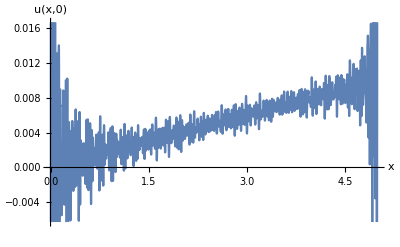

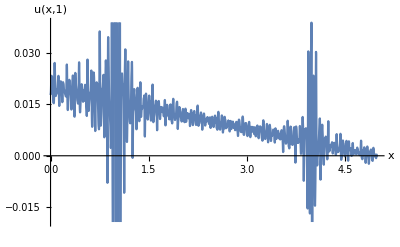

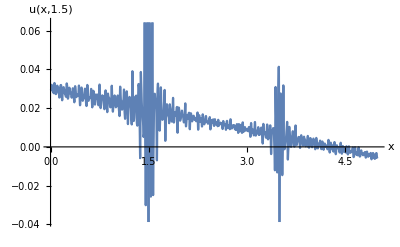

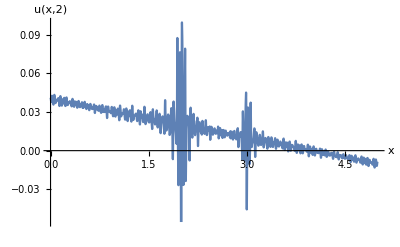

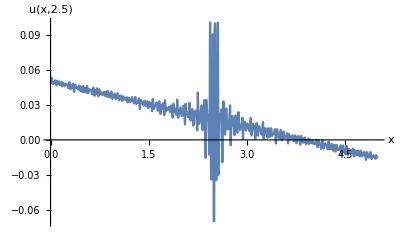

```mathematica
Plot3D[Evaluate[u[x, t]], {x, 0, l}, {t, 0.001, 10},  AxesLabel -> {x, t, "u(x, t)"}, PlotRange -> {Automatic, Automatic} ]

Plot[Evaluate[u[x, 0.01 ]], {x, 0, l},  AxesLabel->{x, "u(x,0)"}, PlotRange->{{0, l}, Automatic} ]

Plot[Evaluate[u[x, 1 ]], {x, 0, l},  AxesLabel->{x, "u(x,1)"}, PlotRange->{{0, l}, Automatic} ]
Plot[Evaluate[u[x, 1.5 ]], {x, 0, l},  AxesLabel->{x, "u(x,1.5)"}, PlotRange->{{0, l}, Automatic} ]
Plot[Evaluate[u[x, 2 ]], {x, 0, l},  AxesLabel->{x, "u(x,2)"},PlotRange->{{0, l}, Automatic} ]
Plot[Evaluate[u[x, 2.5 ]], {x, 0, l},  AxesLabel->{x, "u(x,2.5)"},PlotRange->{{0, l}, Automatic} ]
```